```mathematica
refxc[r_]:= 1/r^2(2 EllipticE[1/Sqrt[2]]-(1+r)/2 EllipticPi[(1-r)/2,1/Sqrt[2]]-(1-r)/2 EllipticPi[(1+r)/2,1/Sqrt[2]])
```

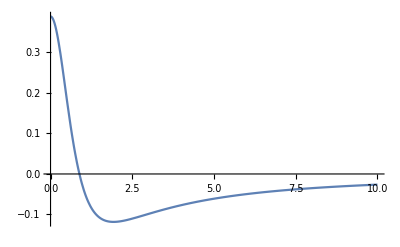

```mathematica
Plot[refxc[Sqrt[1+x^2]],{x,0,10},PlotRange->Full]
```

```mathematica
refxckk[z_]:=NIntegrate[x/(1.+x^2)^(5/4)/(x-z),{x,-Infinity,z,Infinity},Method->PrincipalValue]/Pi
```

```mathematica
dat=Table[{z,refxckk[z]},{z,0,10,.01}];
```

```mathematica
dat2=Import["/Users/aaronkaplan/Dropbox/phd.nosync/mcp07_revised/code/test_fits/kram_kron_re_fxc.csv","Data"];
```

```mathematica
dat2=Import["/Users/aaronkaplan/Dropbox/phd.nosync/tddft_ultranonlocality/re_fxc_dimensionless.csv","Data"];
```

```mathematica
dat3=Table[{dat2[[i,1]],dat2[[i,2]]},{i,2,Length[dat2]}];
```

```mathematica
diff = Table[{dat3[[i,1]],Abs[dat3[[i,2]]-dat[[i,2]]]},{i,1,Length[dat3]}];
```

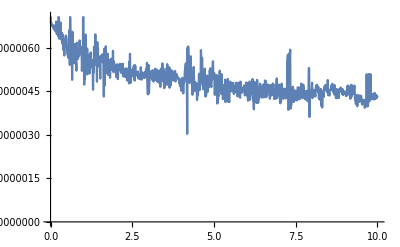

```mathematica
ListPlot[diff,Joined->True]
```

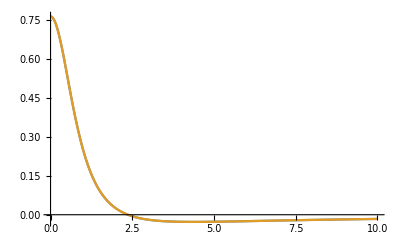

```mathematica
ListPlot[{dat,dat3},Joined->True,PlotRange->Full]
```

```mathematica
γ=1.311028777146059809410871821455657482147216796875;
h[x_,a_,b_,c_]:=1/γ(1-a x^2)/ (1+b x^2 +(a/γ)^(2c/7) x^c)^(7/(2c))
```

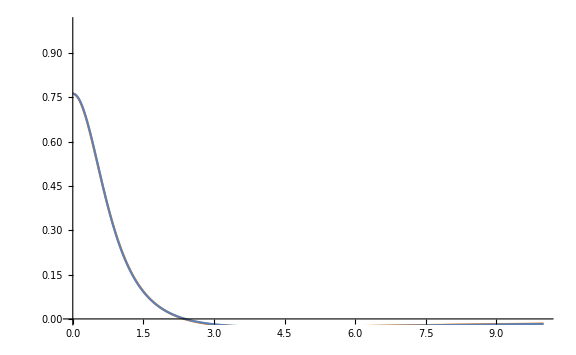

```mathematica
Show[{ListPlot[dat3,PlotStyle->Orange,Joined->True,PlotRange->Full],Plot[h[x,0.1756,1.0376,2.9787],{x,0,10},PlotRange->Full]},PlotRange->{{0,10},{0,1}},ImageSize->Large]
```